Loading The Code

```mathematica
Clear @ Evaluate[Context[]<>"*"]
SetDirectory[NotebookDirectory[]]
Get["Utilities.m"]
Get["MeltCurves.m"]
Get["FractionBound.m"]
```

C:\nadir\PCRModelling\MeltCurves

E16082201

#### Loading the Data

```mathematica
Get["MeltCurves`"]
dir = "C:\\Users\\bob\\Dropbox\\Grad School\\Lutz Lab\\FlatmerAnalysis\\";
e16082201 = loadMeltCurves[dir <> "E16082201.xlsx", 6];
e16082201["headerNames"]
data = datasetFromMeltCurves[e16082201, 
Function[{assoc}, hybridize[assoc["R16082205"] // Round, assoc["R16061005"] // Round, assoc["Well Conc (ng/uL)"]]],
Function[{header}, {
"concentration" -> header["Well Conc (ng/uL)"],
"R16082205" -> header["R16082205"],
"R16061005" -> header["R16061005"]
}]
];
```

{Well,Dilution,R16082205,R16061005,Well Conc (M),Well Conc (ng/uL)}

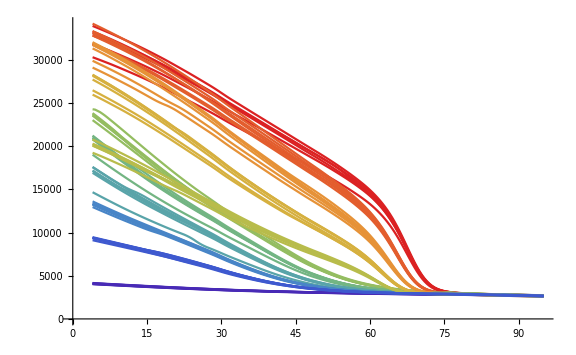

```mathematica
Get["MeltCurves`"]
plotMeltCurves[data]
```

#### Extracting Replicates

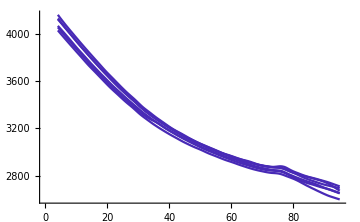

```mathematica
Get["MeltCurves`"]
replicates = groupMeltCurvesByReplicates[data];
blanks = hybridize[0,0,0.] /. replicates;
plotMeltCurves[blanks, ImageSize -> Medium]
```